## 135Pr

```mathematica
ClearAll["Global`*"]
```

```mathematica
yrastEn=Sort[{8760,7803,6880.5,5998.8,5164.9,4320.9,3245.4,2245.3,1391.1,730.9,358.08}];
wob1En=Sort[{5067.5,3955.5,2999.9,2203.9,1477.9}];
wob2En=Sort[{1928.08,2692.08,2755.08,2937.08}];
purewob2={826.3,763.8,1009.0}/2000;
yrastSpin=Table[i/2,{i,11,55,4}];
wob1Spin=Table[i/2,{i,17,33,4}];
wob2Spin=Table[i/2,{i,19,31,4}];
```

```mathematica
omega[data_]:=Table[1/2(data[[i]]-data[[i-1]])/1000,{i,2,Length[data]}];
```

```mathematica
omegaYrast=omega[yrastEn];
omegawob1=omega[wob1En];
omegawob2=omega[wob2En];
```

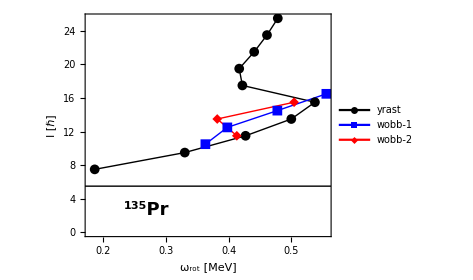

```mathematica
fig=ListPlot[{Table[{omegaYrast[[i]],yrastSpin[[i+1]]},{i,1,Length[omegaYrast]}],Table[{omegawob1[[i]],wob1Spin[[i+1]]},{i,1,Length[omegawob1]}],Table[{purewob2[[i]],wob2Spin[[i+1]]},{i,1,Length[purewob2]}]},Joined->True,PlotMarkers->{Automatic, Medium},AspectRatio->0.8,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"ω_rot [MeV]","I [ℏ]"},LabelStyle->{18,Bold,Black,FontFamily->"Times"},PlotRange->Full,ImageSize->350,FrameTicks->{{Automatic,None},{{0.2,0.3,0.4,0.5},None}},Epilog->{Style[Line[{{-100,5.5},{100,5.5}}],Thick,Magenta,DotDashed,Opacity[1]],Inset[Style[Framed[Row[{Superscript["","135"],"Pr"}]],FontFamily->"Times",Black,18,Bold],Scaled[{0.25,0.12}]]},PlotStyle->{{Black,Thick},{Blue,Thick},{Red,Thick}},PlotLegends->Placed[{"yrast","wobb-1","wobb-2"},{0.25,0.75}]];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/135Pr_wob.pdf",fig];
Show[fig]
```

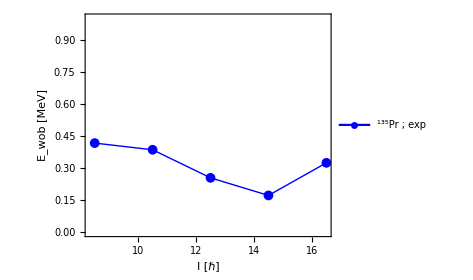

```mathematica
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2(yrast[[i+1]]+yrast[[i+2]])/1000},{i,1,Length[b1]}];
data=wobbling[yrastEn,wob1En,wob1Spin];
fig2=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{20,Bold,Black},PlotLegends->Placed[{Style[Row[{Superscript["","135"],"Pr ; exp"}],30]},{0.4,0.85}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/135Pr.pdf",fig2];
Show[fig2]
```